```mathematica
ep=0.08;β=0.8;γ=0.5;
τ=131.56;α=0.081;γt=1.6221;
xmin=-50;xmax=50;maxtime=100; dd1=2;dd2=0.001;δ=7.5;
eqn=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
{v0,w0}={v,(v+β)/γ}/.eqn;
d2=1;d1=0.5;
ρ[x_]=d2*d1^(3/2)/(d1+x^2)^(3/2);(*no block*)
(*ρ1=0.7;slope=0.2;
ρ[x_]=Which[x<0,0,x<ρ1/slope,x * slope,x<2ρ1/slope, 2ρ1-x*slope, True,0];
ρ[x_]=ρ1;*)
(*ρ[x_]=Which[x<0,0,x<ρ1/slope,x * slope,True,ρ1];*)
(*eqn1=FindRoot[(1-ρ1^2/2)v-v^3/3-(v+β)/γ,{v,-1}];*)
eqn1=FindRoot[v-v^3/3-(v+β)/γ,{v,-1}];
{v1,w1}={v,(v+β)/γ}/.eqn1;
If[1-v0^2<Min[ep γ,1/γ],"(v0,w0) is locally exponentially stable"]
(*If[1-(v1/Sqrt[1-ρ1^2/2])^2<Min[ep γ /(1-ρ1^2/2)^2,Sqrt[1-ρ1^2/2]/γ],"(v1,w1) is locally exponentially stable"]*)
```

(v0,w0) is locally exponentially stable

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

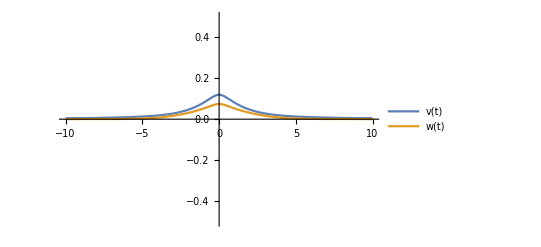

NDSolveValue::mxsst: Using maximum number of grid points 10000 allowed by the MaxPoints or MinStepSize options for independent variable x.

-Graphics3D-

```mathematica
(*Step 1: Starting from the equilibrium, lead to an ok initial guess*)
{V1,W1}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-u[t,x])(u[t,x]-α)+(1+α-3u[t,x])ρ[x]^2/2- w[t,x], τ D[w[t, x], t] == u[t, x] - γt w[t, x], 
u[0, x] ==0, 
u[t, xmin] == 0, 
u[t, xmax] == 0, w[0, x] ==0}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
{V2,W2}=NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-u[t,x])(u[t,x]-α)+(1+α-3u[t,x])ρ[x]^2/2- w[t,x], τ D[w[t, x], t] == u[t, x] - γt w[t, x], 
u[0, x] ==V1[maxtime,x], 
u[t, xmin] == 0, 
u[t, xmax] == 0, w[0, x] ==W1[maxtime,x]}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot[{V2[maxtime,x],W2[maxtime,x]},{x,-10,10},PlotRange->{-0.5,0.5},PlotLegends->{"v(t)","w(t)"}]
(*Step 3: First approximation to autonomus solution, uses previous iteration*)
{V3,W3}=
NDSolveValue[{D[u[t, x], t] == dd1 D[u[t, x], x, x] + u[t, x](1-u[t,x])(u[t,x]-α)+(1+α-3u[t,x])ρ[x]^2/2- w[t,x], τ D[w[t, x], t] == u[t, x] - γt w[t, x], 
u[0, x] ==V2[maxtime,x]+Which[Abs[x-6] <=2, 0.85, True, 0],
u[t, xmin] == 0, 
u[t, xmax] == 0, w[0, x] ==W2[maxtime,x]}, {u, w}, {t, 0, maxtime}, {x, xmin, xmax}];
Plot3D[{V3[t,x]}, {t, 0, maxtime}, {x, xmin, xmax},PlotRange->{-2,2},AxesLabel->{"time","space"},Mesh->All]
```

```mathematica
Animate[Plot[{V3[t,x]-V2[maxtime,x],W3[t,x]-W2[maxtime,x]},{x,xmin,xmax},PlotRange->{-1,2}],{t,0,maxtime},AnimationRunning->False,AnimationRepetitions->1]
```

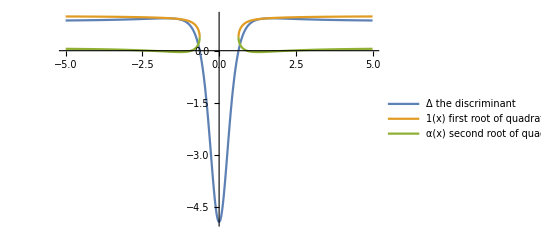

```mathematica
(*P1 and P2 are the root in the factorization after the change of variables*)
g[x_]=(1+α-3V2[maxtime,x])^2-4(α+3V2[maxtime,x]^2-2(1+α )V2[maxtime,x]+3ρ[x]^2/2);
p1[x_]=0.5(1+α-3V2[maxtime,x])+0.5Sqrt[(1+α-3V2[maxtime,x])^2-4(α+3V2[maxtime,x]^2-2(1+α )V2[maxtime,x]+3ρ[x]^2/2)];
p2[x_]=0.5(1+α-3V2[maxtime,x])-0.5Sqrt[(1+α-3V2[maxtime,x])^2-4(α+3V2[maxtime,x]^2-2(1+α )V2[maxtime,x]+3ρ[x]^2/2)];
Plot[{g[x],p1[x],p2[x]},{x,-5,5},PlotRange->All,PlotLegends->{"Δ the discriminant","1(x) first root of quadratic ","α(x) second root of quadratic"}]
```

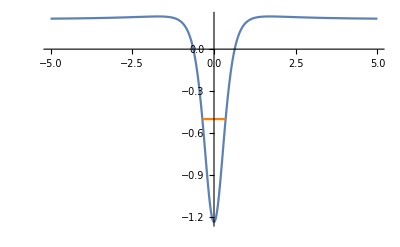

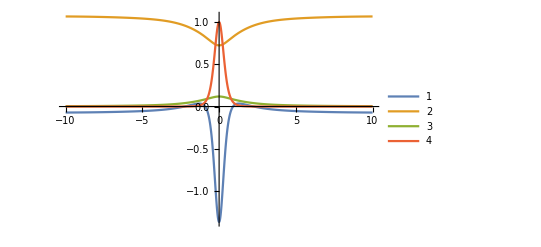

```mathematica
(*Maximum of the quadratic polynomial with coefficientes P1 and P2*)
a1[x_]=-α+2V2[maxtime,x](1+α)-3V2[maxtime,x]^2-3ρ[x]^2/2;
a2[x_]=1+α-3V2[maxtime,x];
(*the maximum of a quadratic is (4ac-b^2)/(4a) *)
g1=Plot[(4a1[x]+a2[x]^2)/4,{x,-5,5},PlotRange->All];
g2=Plot[-0.5,{x,-0.35,0.35},PlotStyle->Orange];
Show[g1,g2]
Plot[{a1[x],a2[x],V2[maxtime,x],ρ[x]^2},{x,-10,10},PlotLegends->Automatic]
```

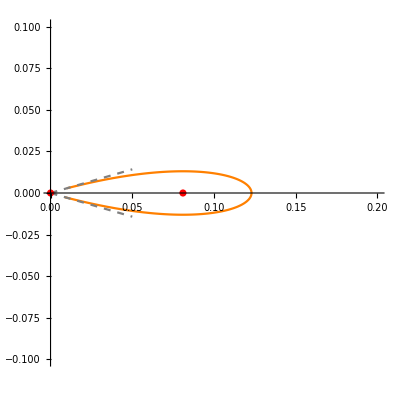

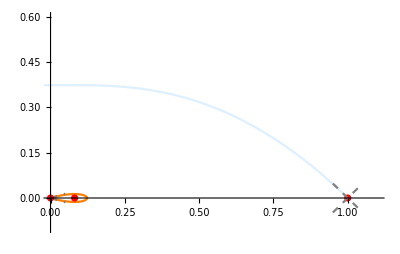

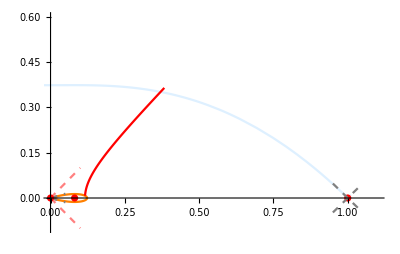

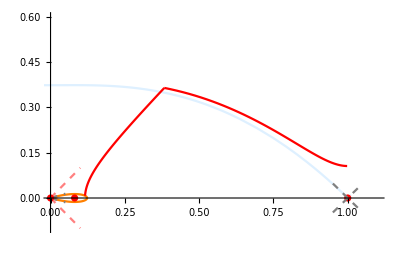

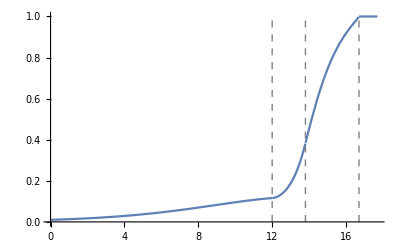

```mathematica
(*Search For homoclinic of (0,0)*)
simulationTime=28;
{Ux0,Vx0}=NDSolveValue[{u'[x]==v[x],-v'[x]==u[x](u[x]-α)(1-u[x]),u[0]==0.01,v[0]==Sqrt[α]0.01},{u,v},{x,0,simulationTime}];
g1=ParametricPlot[{Ux0[x],Vx0[x]},{x,0,simulationTime},PlotRange->{{0,0.2},{-0.1,0.1}},PlotStyle->Orange];
g2=ListPlot[{{0,0},{α,0},{1,0}},PlotStyle->Red];
g3 =Plot[{Sqrt[α]x,-Sqrt[α]x},{x,0,0.05},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
Show[g1,g2,g3]
(*Search For Stable Manifold of (1,0)*)
simulationTime=6;
{Ux,Vx}=NDSolveValue[{u'[x]==v[x],-v'[x]==u[x](u[x]-α)(1-u[x]),u[0]==1-0.01,v[0]==Sqrt[1-α]0.01},{u,v},{x,-simulationTime,simulationTime}];
g1b=ParametricPlot[{Ux[x],Vx[x]},{x,-simulationTime,simulationTime},PlotRange->{{0,1.1},{-0.1,0.4}},PlotStyle->LightBlue];
g3b =Plot[{Sqrt[1-α](x-1),-Sqrt[1-α](x-1)},{x,0.95,1.05},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
Show[g1,g3,g1b,g2,g3b,PlotRange->{{0,1.1},{-0.1,0.6}}]
(*Shoot with expotential trajectory of the system*)
startTime=12;
gapLength=1.8;
kappa=1;
{Ux3,Vx3}=NDSolveValue[{u'[x]==v[x],-v'[x]==-kappa u[x],u[0]==Ux0[startTime],v[0]==Vx0[startTime]},{u,v},{x,0,gapLength}];
g1c=ParametricPlot[{Ux3[x],Vx3[x]},{x,0,gapLength},PlotRange->{{0,1.1},{-0.1,0.4}},PlotStyle->Red];
g3c =Plot[{Sqrt[kappa]x,-Sqrt[kappa]x},{x,0,0.1},PlotStyle->{{Pink,Dashed},{Pink,Dashed}}];
Show[g1,g3,g1b,g2,g3b,g1c,g3c,PlotRange->{{0,1.1},{-0.1,0.6}}]

(*Continue with standard trajectory*)
simulationTime2=2.9;
kappa=1;
{Ux4,Vx4}=NDSolveValue[{u'[x]==v[x],-v'[x]==u[x](u[x]-α)(1-u[x]),u[0]==Ux3[gapLength],v[0]==Vx3[gapLength]},{u,v},{x,0,simulationTime2}];
g1d=ParametricPlot[{Ux4[x],Vx4[x]},{x,0,simulationTime2},PlotRange->{{0,1.1},{-0.1,0.4}},PlotStyle->Red];
Show[g1,g3,g1b,g2,g3b,g1c,g3c,g1d,PlotRange->{{0,1.1},{-0.1,0.6}}]

g0=Plot[Which[x<startTime,Ux0[x],x<startTime+gapLength,Ux3[x-startTime],x<startTime+gapLength+simulationTime2,Ux4[x-(startTime+gapLength)],True,1],{x,0,startTime+gapLength+simulationTime2+1},PlotRange->{0,1}];
lines=Graphics[{Directive[Gray,Dashed,Thick],Line[{{startTime,0},{startTime,1}}],
Directive[Gray,Dashed,Thick],Line[{{startTime+gapLength,0},{startTime+gapLength,1}}],
Directive[Gray,Dashed,Thick],Line[{{startTime+gapLength+simulationTime2,0},{startTime+gapLength+simulationTime2,1}}]}];
Show[g0,lines]
```

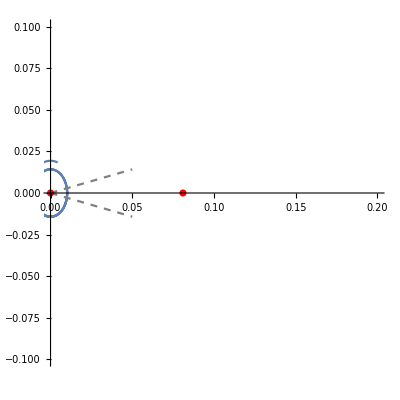

```mathematica
(*AGAIN BUT WITH VARIABLE COEFFICIENTS*)
(*Search For homoclinic of (0,0)*)
a1[x_]=-α+2V2[maxtime,x](1+α)-3V2[maxtime,x]^2-3ρ[x]^2/2;
a2[x_]=1+α-3V2[maxtime,x];
simulationTime=22;
startingPoint=-11;
{Ux0,Vx0}=NDSolveValue[{u'[x]==v[x],-v'[x]==u[x](a1[x+startingPoint]+a2[x+startingPoint]u[x]-u[x]^2)+1/γt u[x],u[0]==0.01,v[0]==Sqrt[α-1/γt]0.01},{u,v},{x,0,2-startingPoint}];
g1=ParametricPlot[{Ux0[x],Vx0[x]},{x,0,2-startingPoint},PlotRange->{{0,0.2},{-0.1,0.1}}];
g2=ListPlot[{{0,0},{α,0},{1,0}},PlotStyle->Red];
g3 =Plot[{Sqrt[α]x,-Sqrt[α]x},{x,0,0.05},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
Show[g1,g2,g3]
(*
(*Search For Stable Manifold of (1,0)*)
simulationTime=6;
{Ux,Vx}=NDSolveValue[{u'[x]==v[x],-v'[x]==u[x](u[x]-α)(1-u[x]),u[0]==1-0.01,v[0]==Sqrt[1-α]0.01},{u,v},{x,-simulationTime,simulationTime}];
g1b=ParametricPlot[{Ux[x],Vx[x]},{x,-simulationTime,simulationTime},PlotRange->{{0,1.1},{-0.1,0.4}},PlotStyle->LightBlue];
g3b =Plot[{Sqrt[1-α](x-1),-Sqrt[1-α](x-1)},{x,0.95,1.05},PlotStyle->{{Gray,Dashed},{Gray,Dashed}}];
Show[g1,g3,g1b,g2,g3b,PlotRange->{{0,1.1},{-0.1,0.6}}]
(*Shoot with expotential trajectory of the system*)
startTime=12;
gapLength=1.8;
kappa=1;
{Ux3,Vx3}=NDSolveValue[{u'[x]==v[x],-v'[x]==-kappa u[x],u[0]==Ux0[startTime],v[0]==Vx0[startTime]},{u,v},{x,0,gapLength}];
g1c=ParametricPlot[{Ux3[x],Vx3[x]},{x,0,gapLength},PlotRange->{{0,1.1},{-0.1,0.4}},PlotStyle->Red];
g3c =Plot[{Sqrt[kappa]x,-Sqrt[kappa]x},{x,0,0.1},PlotStyle->{{Pink,Dashed},{Pink,Dashed}}];
Show[g1,g3,g1b,g2,g3b,g1c,g3c,PlotRange->{{0,1.1},{-0.1,0.6}}]

(*Continue with standard trajectory*)
simulationTime2=2.9;
kappa=1;
{Ux4,Vx4}=NDSolveValue[{u'[x]==v[x],-v'[x]==u[x](u[x]-α)(1-u[x]),u[0]==Ux3[gapLength],v[0]==Vx3[gapLength]},{u,v},{x,0,simulationTime2}];
g1d=ParametricPlot[{Ux4[x],Vx4[x]},{x,0,simulationTime2},PlotRange->{{0,1.1},{-0.1,0.4}},PlotStyle->Red];
Show[g1,g3,g1b,g2,g3b,g1c,g3c,g1d,PlotRange->{{0,1.1},{-0.1,0.6}}]

g0=Plot[Which[x<startTime,Ux0[x],x<startTime+gapLength,Ux3[x-startTime],x<startTime+gapLength+simulationTime2,Ux4[x-(startTime+gapLength)],True,1],{x,0,startTime+gapLength+simulationTime2+1},PlotRange->{0,1}];
lines=Graphics[{Directive[Gray,Dashed,Thick],Line[{{startTime,0},{startTime,1}}],
Directive[Gray,Dashed,Thick],Line[{{startTime+gapLength,0},{startTime+gapLength,1}}],
Directive[Gray,Dashed,Thick],Line[{{startTime+gapLength+simulationTime2,0},{startTime+gapLength+simulationTime2,1}}]}];
Show[g0,lines]
*)
```

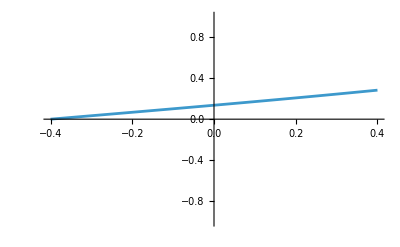

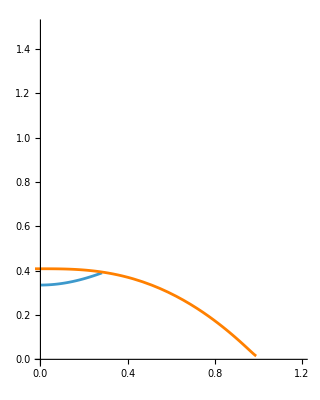

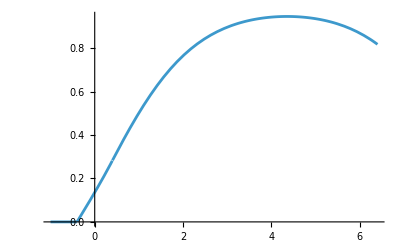

```mathematica
p=-0.4;
alph=0.5;
initialSlope=0.335;
innerRegion=0.4;
g0=Plot[Which[x>p,initialSlope (1/Sqrt[alph])Sinh[Sqrt[alph](x-p)],True,0],{x,-innerRegion,innerRegion},PlotRange->{-1,1}]
g1=ParametricPlot[{initialSlope (1/Sqrt[alph])Sinh[Sqrt[alph](x-p)],initialSlope Cosh[Sqrt[alph](x-p)]},{x,p,innerRegion},PlotRange->{{0,1.2},{0,1.5}}];
{Ux,Vx}=NDSolveValue[{-u'[x]==v[x],v'[x]==u[x]^2(1-u[x]),u[0]==0.99,v[0]==0.015},{u,v},{x,0,6}];
g2=ParametricPlot[{Ux[x],Vx[x]},{x,0,6},PlotRange->{{0,1.2},{0,1.5}},PlotStyle->Orange];
Show[g1,g2]
{Ux2,Vx2}=NDSolveValue[{u'[x]==v[x],-v'[x]==u[x]^2(1-u[x]),u[0]==initialSlope (1/Sqrt[alph])Sinh[Sqrt[alph](innerRegion-p)],v[0]==initialSlope Cosh[Sqrt[alph](innerRegion-p)]},{u,v},{x,0,6}];
vv[x_]=Which[x<p,0,x<innerRegion,initialSlope (1/Sqrt[alph])Sinh[Sqrt[alph](x-p)],True,Ux2[x-innerRegion]];
Plot[vv[x],{x,-1,innerRegion+6}]
```

0.05

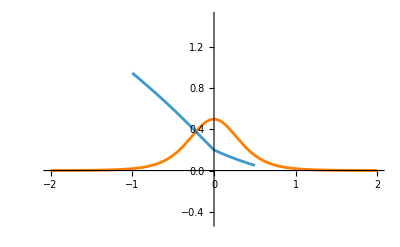

```mathematica
a1[x_]=-α+2V2[maxtime,x](1+α)-3V2[maxtime,x]^2-3ρ[x]^2/2;
a2[x_]=1+α-3V2[maxtime,x];
alpha = -1;
alpha2=0.5;
startingValue=0.95;
value0=0.2;
startingSlope=-0.1;
finalSlope=-0.2;
finalValue=0.05
Ushoot1=NDSolveValue[{-u''[x]==u[x](1-u[x])(u[x]-α)-(1+α-3u[x])ρ[x]^2/2,u[alpha]==startingValue,u[0]==value0},u,{x,alpha,0}];
Ushoot2=NDSolveValue[{-u''[x]==u[x](1-u[x])(u[x]-α)-(1+α-3u[x])ρ[x]^2/2,u[0]==value0,u[alpha2]==finalValue},u,{x,0,alpha2}];
g3=Plot[ρ[x]^2/2,{x,-2,2},PlotStyle->Orange,PlotRange->{{-2,2},{-0.5,1.5}}];
g1=Plot[Ushoot1[x],{x,alpha,0},PlotRange->{{-0.5,1.5}}];
g2=Plot[Ushoot2[x],{x,0,alpha2},PlotRange->{-0.5,1.5}];

Show[g3,g1,g2]
```